```mathematica
With[{lst=Range[17],k=12},Values@GroupBy[Transpose[{lst,RandomSample[Flatten[{Range[k],RandomSample[Range[k],17-k]}],17]}],Last->First]]
```

{{1,11},{2,9},{3},{4,16},{5},{6},{7},{8},{10},{12,13},{14,17},{15}}

```mathematica
Integrate[1/Sqrt[1-x^2],x]
```

ArcSin[x]

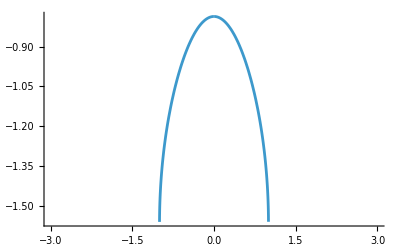

```mathematica
Plot[{%-ArcSin[x^2]},{x,-3,3}]
```

```mathematica
D[ArcSin[x^2],x]
```

(2 x)/(√(1-x^4))

```mathematica
D[1/Log[Cos[x]],x]
```

Tan[x]/Log[Cos[x]]^2

```mathematica
Integrate[Tan[x]/Log[Cos[x]],x]
```

-Log[Log[Cos[x]]]

```mathematica
Expand[-(x+3)(x+4)(x-2)-11]
```

13+2 x-5 x^2-x^3

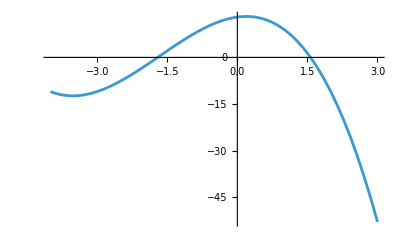

```mathematica
Plot[%,{x,-4,3}]
```

```mathematica
f[x_]:=13+2 x-5 x^2-x^3
fp[x_]:=2=10x-3x^2
```

```mathematica
Clear[l];
x=b;
y=Sqrt[l^2-b^2];
xp=-2/3;
For[l=10,l<=20,l++,Print[FindInstance[-x*xp/y<10&&x∈ Integers,b]]]
```

{{b→0}}

{{b→0}}

{{b→0}}

«8 more identical outputs»

```mathematica
l=15;b=5;y=Sqrt[l^2-b^2];
xp=-1/2
-x*xp/y
```

-1/2

1/(4 √2)

```mathematica
Clear[x]
```

```mathematica
f=Integrate[(x-3)*(x+2),x]
```

-6 x-x^2/2+x^3/3

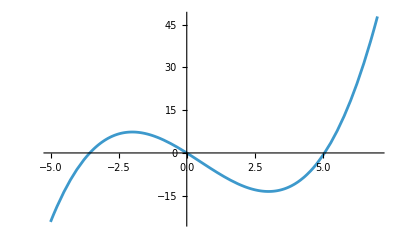

{{x→0},{x→3/4 (1-√33)},{x→3/4 (1+√33)}}

```mathematica
Plot[f,{x,-5,7}]
Solve[f==0,x]
```

```mathematica
D[(x-2)^2  Exp[ x],x]
Simplify[D[%,x]]
```

2 ⅇ^x (-2+x)+ⅇ^x (-2+x)^2

ⅇ^x (-2+x^2)

```mathematica
f=(x-2)^2  Exp[ x]
Simplify[D[f,x]]
Solve[D[f,x]==0,x]
Simplify[D[D[f,x],x]]
```

ⅇ^x (-2+x)^2

ⅇ^x (-2+x) x

{{x→0},{x→2}}

ⅇ^x (-2+x^2)

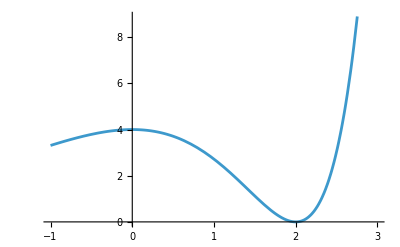

```mathematica
Plot[f,{x,-1,3}]
```

```mathematica
Integrate[x^2-2,x]
```

-2 x+x^3/3

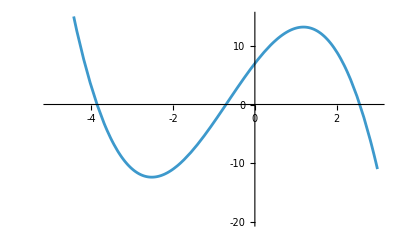

```mathematica
Plot[-x^3-2 x^2+9 x+7,{x,-5,3}, Ticks->{Range[-4,4],Range[-20,15,5]},PlotRange->{-20,15}]
```

```mathematica
Clear[x,f]
f[x_]:=-x^3-5x^2+2x+13
f[x-1]
```

13+2 (-1+x)-5 (-1+x)^2-(-1+x)^3

```mathematica
Expand[%]
```

-x^3-2 x^2+9 x+7